### All “Signed” Permutations of (A,B,C,D,E,F) preserving the system (A+B=C, B+D=F, C+D=E, A+F=E)

```mathematica
(*A+B=C,B+D=F,C+D=E,A+F=E*)
tetra=
{{1,1,-1,0,0,0},
{0,1,0,1,0,-1},
{0,0,1,1,-1,0},
{1,0,0,0,-1,1}};
MatrixForm[tetra]
```

(1 | 1 | -1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | -1
0 | 0 | 1 | 1 | -1 | 0
1 | 0 | 0 | 0 | -1 | 1)

```mathematica
(* All permutations of n elements as n by n {0,1}-valued permutation matrices *)
matrixPerms[n_]:=Map[Permute[IdentityMatrix[n],#]&,GroupElements[SymmetricGroup[n]]];
```

```mathematica
(* All sign flips of n elements as n by n {-1,0,1}-valued  matrices *)
matrixSignFlips[n_]:=Map[DiagonalMatrix,Tuples[{-1,+1},n]];
```

```mathematica
(* All signed permutations of n elements as n by n {-1,0,1}-valued signed permutation matrices *)
matrixSignedPerms[n_]:=ReverseSort[Flatten[Outer[#1.#2&,matrixSignFlips[n],matrixPerms[n],1],1]];
```

```mathematica
(* This finds all of the elements of 'matrixSignedPerms[6]' which factor through the matrix 'tetra' in the sense that 
'matrixSignedPerms[4]⟦j⟧.tetra==tetra.matrixSignedPerms[6]⟦i⟧' holds for some 'j' *)
TetraSignedPermutationMatrixGroup=
Module[{valid,rightSignedPerms,leftSignedPerms,i,j},
valid={};
leftSignedPerms=matrixSignedPerms[4];
rightSignedPerms=matrixSignedPerms[6];
For[i=1,i≤Length[rightSignedPerms],i=i+1,
For[j=1,j≤Length[leftSignedPerms],j=j+1,
If[leftSignedPerms⟦j⟧.tetra==tetra.rightSignedPerms⟦i⟧,
AppendTo[valid,i];Continue[];
]
]
];
rightSignedPerms⟦valid⟧
];
Length[TetraSignedPermutationMatrixGroup]
```

48

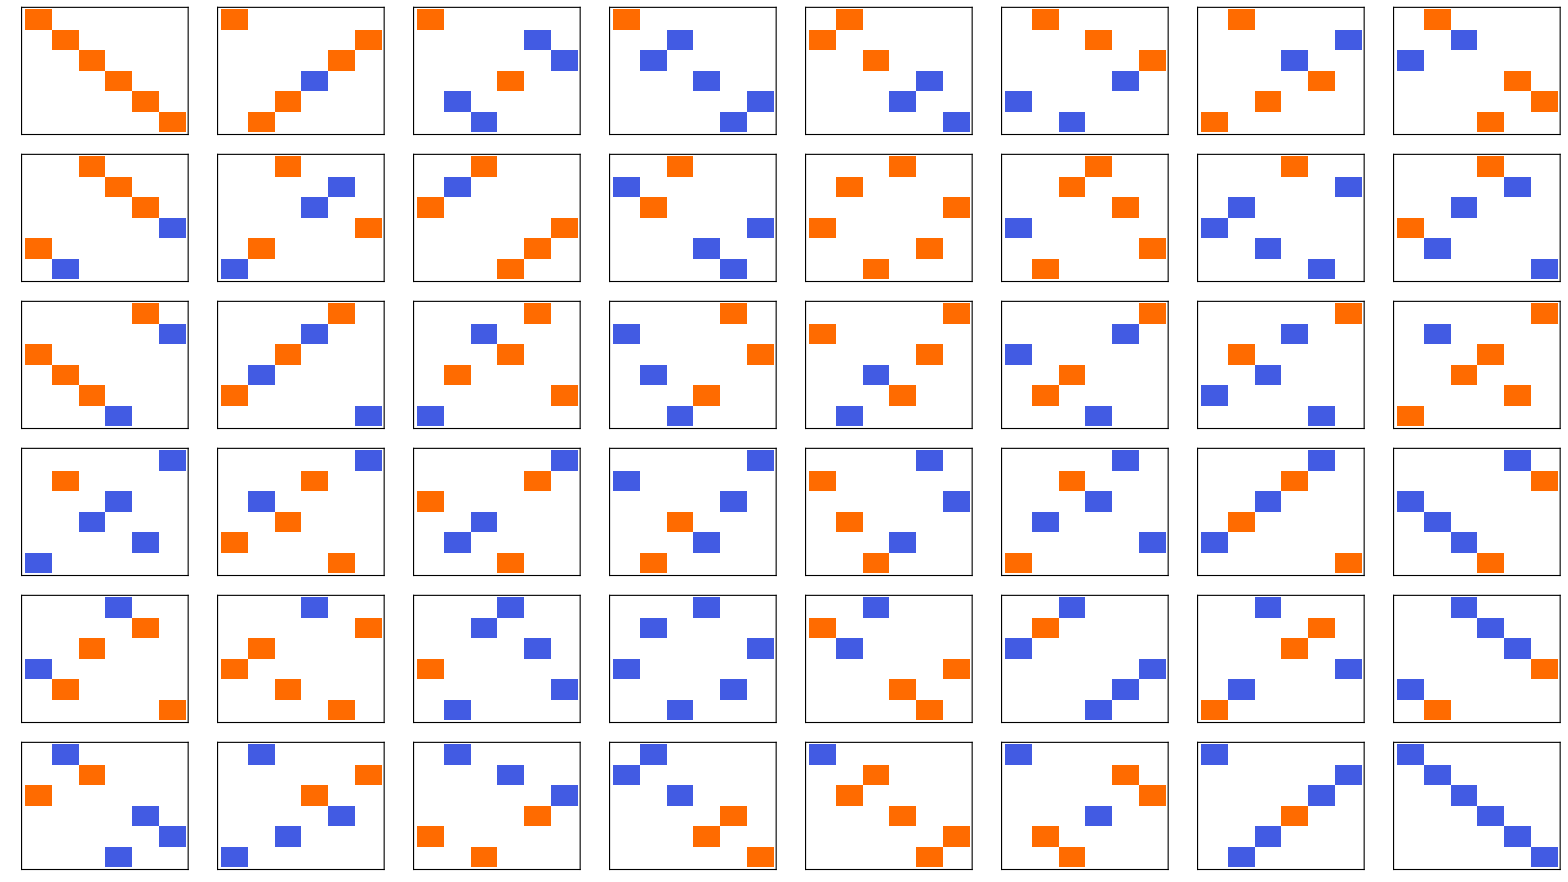

```mathematica
Grid[ArrayReshape[Map[MatrixPlot[#,FrameTicks->None]&,TetraSignedPermutationMatrixGroup],{6,8}]]
```

```mathematica
(* These were chosen manually. One can confirm they generate a group of order 48 and they are all necessary generators. ({2,10},{2,20},{2,27},{2,43})*)
matrixGenerators=TetraSignedPermutationMatrixGroup⟦{2,10}⟧;
Map[MatrixForm,matrixGenerators]
```

{(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixElemToCycles=Function[{g,allGroupElems},PermutationCycles[Map[First[First[Position[TetraSignedPermutationMatrixGroup,#.g]]]&,allGroupElems]]];
cyclesGenerators=Map[MatrixElemToCycles[#,TetraSignedPermutationMatrixGroup]&,matrixGenerators]
```

{Cycles[{{1,2},{3,4},{5,21},{6,23},{7,24},{8,22},{9,18},{10,19},{11,17},{12,20},{13,34},{14,33},{15,36},{16,35},{25,42},{26,43},{27,41},{28,44},{29,37},{30,39},{31,40},{32,38},{45,46},{47,48}}],Cycles[{{1,10,36,27},{2,12,35,26},{3,11,33,25},{4,9,34,28},{5,30,43,17},{6,32,44,19},{7,29,41,18},{8,31,42,20},{13,22,48,39},{14,23,47,37},{15,21,45,40},{16,24,46,38}}]}

```mathematica
TetraSignedPermutationFormalGroup=PermutationGroup[cyclesGenerators];GroupOrder[TetraSignedPermutationFormalGroup]
```

48

```mathematica
CayleyGraph[TetraSignedPermutationFormalGroup]
```

-Graphics-

```mathematica
candidateRelations=Module[{adj,order2Edges,order4Edges,fundamentalCycles},
adj=Normal[AdjacencyMatrix[Map[Apply[UndirectedEdge,#]&,EdgeList[CayleyGraph[TetraSignedPermutationFormalGroup]]]]];
order2Edges=Map[Apply[UndirectedEdge],Position[adj,2]];
order4Edges=Map[Apply[UndirectedEdge],Position[adj,1]];
fundamentalCycles=FindFundamentalCycles[AdjacencyGraph[adj/.{2->1}]];
DeleteDuplicates[Map[If[MemberQ[order2Edges,#],"a","b"]&,fundamentalCycles,{2}]]
]
```

{{b,b,b,b},{a,b,a,b,b,a,b,a,b,b},{b,a,b,a,b,a,b,a,b,a,b,a},{b,b,a,b,b,a,b,b,a,b,b,a},{b,a,b,b,a,b,a,b,b,a},{b,a,b,a,b,b,a,b,a,b}}

```mathematica
relations={{"a","a"},{"b","b","b","b"},{"a","b","a","b","b","a","b","a","b","b"},{"a","b","a","b","a","b","a","b","a","b","a","b"},{"a","b","b","a","b","b","a","b","b","a","b","b"},{"b","a","b","a","b","b","a","b","a","b"}}
```

{{a,a},{b,b,b,b},{a,b,a,b,b,a,b,a,b,b},{a,b,a,b,a,b,a,b,a,b,a,b},{a,b,b,a,b,b,a,b,b,a,b,b},{b,a,b,a,b,b,a,b,a,b}}

```mathematica
{a^2,b^4,(a*b*a*b^2)^2,(a*b)^6,(a*b^2)^4,(b*a*b*a*b)^2};
```

```mathematica
genA=TetraSignedPermutationMatrixGroup⟦2⟧;genB=TetraSignedPermutationMatrixGroup⟦10⟧;
```

```mathematica
(* All of the relations hold! *)
Map[MatrixForm[Apply[Dot,#]]&, relations/.{"a"->genA,"b"->genB}]
```

{(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)}

# This is SageMath code to confirm the identity of the group against GAP’s standard ordering

F.<a,b> = FreeGroup()
R = [a^2,b^4,(a*b)^6,(b*a*b*a*b)^2]
G = (F / R).as_permutation_group()
print(“Order of G is”, len(G))

# GAP’s AllSmallGroups produces list of groups of order 48
gap_groups = [PermutationGroup(gap_group=K.AsPermGroup()) for K in gap(48).AllSmallGroups()]
print(“There are”, len(gap_groups), “finite groups of order 48.”)

# Print the groups
for i,K in enumerate(gap_groups):
    if (K.is_isomorphic(G)):
        print(“G is isomorphic to GAP’s”, i+1, “-th group of order 48”)
        
print(“Confirmation:”, G.is_isomorphic(PermutationGroup(gap_group=gap(48).SmallGroup(48).AsPermGroup())))

```mathematica
matrixGenerators.{"A","B","C","D","E","F"}//MatrixForm
```

(A | F | E | -D | C | B
C | -E | -D | F | B | -A)

```mathematica
conjugacyClasses=Sort[GroupOrbits[TetraSignedPermutationFormalGroup,GroupElements[TetraSignedPermutationFormalGroup],Function[{x,g},PermutationProduct[InversePermutation[g],PermutationProduct[x,g]]]]];
Map[Length,conjugacyClasses]
```

{1,1,3,3,6,6,6,6,8,8}

```mathematica
conjugacyClassToEigenvalueAction[conjClass_]:=MatrixForm[TetraSignedPermutationMatrixGroup⟦Map[First[First[Position[Map[MatrixElemToCycles[#,TetraSignedPermutationMatrixGroup]&,TetraSignedPermutationMatrixGroup],#]]]&,conjClass]⟧.{α,β,γ,δ,ϵ,ϕ}/.{-α->SuperStar[α],-β->SuperStar[β],-γ->SuperStar[γ],-δ->SuperStar[δ],-ϵ->SuperStar[ϵ],-ϕ->SuperStar[ϕ]}]
```

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦1⟧]
```

(α | β | γ | δ | ϵ | ϕ)

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦9⟧]
```

(β | ϕ^* | δ^* | ϵ | γ | α
γ | α^* | β | ϕ^* | δ^* | ϵ^*
ϵ | γ^* | δ | β | ϕ | α^*
ϕ | α | ϵ | γ^* | δ | β^*
ϕ^* | δ | β^* | γ | α | ϵ
ϵ^* | ϕ | α^* | β^* | γ^* | δ
γ^* | δ^* | ϵ^* | ϕ | α^* | β
β^* | γ | α | ϵ^* | ϕ^* | δ^*)

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦2⟧]
```

(α^* | β^* | γ^* | δ^* | ϵ^* | ϕ^*)

```mathematica
conjugacyClassToEigenvalueAction[ReverseSort[conjugacyClasses⟦10⟧]]
```

(β^* | ϕ | δ | ϵ^* | γ^* | α^*
γ^* | α | β^* | ϕ | δ | ϵ
ϵ^* | γ | δ^* | β^* | ϕ^* | α
ϕ^* | α^* | ϵ^* | γ | δ^* | β
ϕ | δ^* | β | γ^* | α^* | ϵ^*
ϵ | ϕ^* | α | β | γ | δ^*
γ | δ | ϵ | ϕ^* | α | β^*
β | γ^* | α^* | ϵ | ϕ | δ)

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦3⟧]
```

(α | ϵ^* | ϕ^* | δ | β^* | γ^*
δ | β | ϕ | α | ϵ | γ
δ^* | ϵ | γ | α^* | β | ϕ)

```mathematica
conjugacyClassToEigenvalueAction[ReverseSort[conjugacyClasses⟦4⟧]]
```

(α^* | ϵ | ϕ | δ^* | β | γ
δ^* | β^* | ϕ^* | α^* | ϵ^* | γ^*
δ | ϵ^* | γ^* | α | β^* | ϕ^*)

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦5⟧]
```

(β | δ | ϕ | ϵ^* | α^* | γ^*
δ | ϕ^* | β^* | α^* | γ^* | ϵ^*
ϕ | ϵ^* | α^* | γ | β | δ^*
ϵ^* | α | ϕ^* | β | δ^* | γ
δ^* | γ^* | ϵ^* | α | ϕ^* | β^*
γ^* | ϵ | δ | ϕ^* | β^* | α)

```mathematica
conjugacyClassToEigenvalueAction[ReverseSort[conjugacyClasses⟦6⟧]]
```

(β^* | δ^* | ϕ^* | ϵ | α | γ
δ^* | ϕ | β | α | γ | ϵ
ϕ^* | ϵ | α | γ^* | β^* | δ
ϵ | α^* | ϕ | β^* | δ | γ^*
δ | γ | ϵ | α^* | ϕ | β
γ | ϵ^* | δ^* | ϕ | β | α^*)

```mathematica
conjugacyClassToEigenvalueAction[conjugacyClasses⟦8⟧]
```

(α | γ^* | β^* | δ^* | ϕ^* | ϵ^*
β | α | γ | ϵ^* | δ^* | ϕ^*
ϕ | β^* | δ | γ | ϵ | α
ϵ^* | δ | γ^* | β | α^* | ϕ
γ^* | β | α^* | ϕ^* | ϵ^* | δ^*
α^* | ϕ^* | ϵ^* | δ | γ^* | β^*)

```mathematica
conjugacyClassToEigenvalueAction[ReverseSort[conjugacyClasses⟦7⟧]]
```

(α^* | γ | β | δ | ϕ | ϵ
β^* | α^* | γ^* | ϵ | δ | ϕ
ϕ^* | β | δ^* | γ^* | ϵ^* | α^*
ϵ | δ^* | γ | β^* | α | ϕ^*
γ | β^* | α | ϕ | ϵ | δ
α | ϕ | ϵ | δ^* | γ | β)